data is from here
https://www.ecdc.europa.eu/en/geographical-distribution-2019-ncov-cases

```mathematica
data={1900+FromDate[DateList[#[[1]]]]/(365.24*3600*24),#[[3]],#[[2]],#[[6]]}&/@Drop[Import["C:\\Users\\Jason Smith\\Desktop\\ECONDATA\\COVID-19-geographic-disbtribution-worldwide-2020-03-08.xls"][[1]],1];
```

```mathematica
totals={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[data[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
```

```mathematica
accumulated=Transpose[{totals[[All,1]],Accumulate[totals[[All,2]]]}];
```

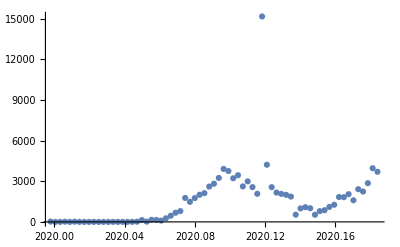

```mathematica
ListPlot[totals,PlotRange->All]
```

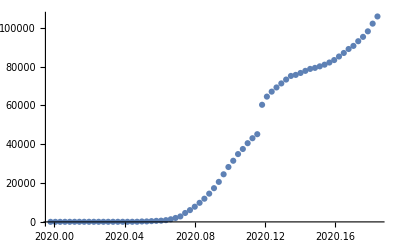

```mathematica
ListPlot[accumulated,PlotRange->All]
```

```mathematica
fitData=Cases[accumulated,x_/;x[[1]]≤2020.116]
nlm=NonlinearModelFit[fitData,a0/(1+Exp[-(t-t0)/b0]),
{
{a0,50000},{b0,0.05},{t0,2020.1}
},t]
```

{{2020.,27.},{2020.,27.},{2020.,27.},{2020.01,44.},{2020.01,44.},{2020.01,59.},{2020.01,59.},{2020.02,59.},{2020.02,59.},{2020.02,59.},{2020.03,59.},{2020.03,59.},{2020.03,59.},{2020.03,60.},{2020.04,60.},{2020.04,61.},{2020.04,61.},{2020.04,66.},{2020.05,83.},{2020.05,219.},{2020.05,239.},{2020.06,392.},{2020.06,534.},{2020.06,631.},{2020.06,897.},{2020.07,1350.},{2020.07,2023.},{2020.07,2820.},{2020.07,4587.},{2020.08,6067.},{2020.08,7823.},{2020.08,9826.},{2020.09,11946.},{2020.09,14554.},{2020.09,17372.},{2020.09,20615.},{2020.1,24522.},{2020.1,28273.},{2020.1,31491.},{2020.1,34933.},{2020.11,37552.},{2020.11,40540.},{2020.11,43105.},{2020.12,45177.}}

FittedModel[51721.8/(1+ⅇ^(103.155 («19»-t)))]

```mathematica
fitData2=Cases[accumulated,x_/;x[[1]]>2020.116]
nlm2=NonlinearModelFit[Drop[fitData2,1],a0/(1+Exp[-(t-t0)/b0])+a1/(1+Exp[-(t-t1)/b1]),
{
{a0,75666.14697988438},{b0,1/112.7406242528004},{t0,2020.1065903285187},
{a1,158316.10070185905},{b1,1/59.02618015129843},{t1,2020.20856169607}
},t]

transitions={t0,t1}/.nlm2["BestFitParameters"]
```

{{2020.12,60328.},{2020.12,64543.},{2020.12,67103.},{2020.13,69265.},{2020.13,71332.},{2020.13,73327.},{2020.13,75191.},{2020.14,75723.},{2020.14,76719.},{2020.14,77804.},{2020.15,78812.},{2020.15,79339.},{2020.15,80132.},{2020.15,80995.},{2020.16,82101.},{2020.16,83365.},{2020.16,85203.},{2020.16,87024.},{2020.17,89068.},{2020.17,90663.},{2020.17,93076.},{2020.18,95315.},{2020.18,98171.},{2020.18,102132.},{2020.18,105828.}}

FittedModel[76273.3/(1+ⅇ^(106.075 («19»-t)))+129360./(1+ⅇ^(62.6001 («19»-t)))]

{2020.11,2020.2}

```mathematica
bands90=nlm2["SinglePredictionBands",ConfidenceLevel->0.5];
```

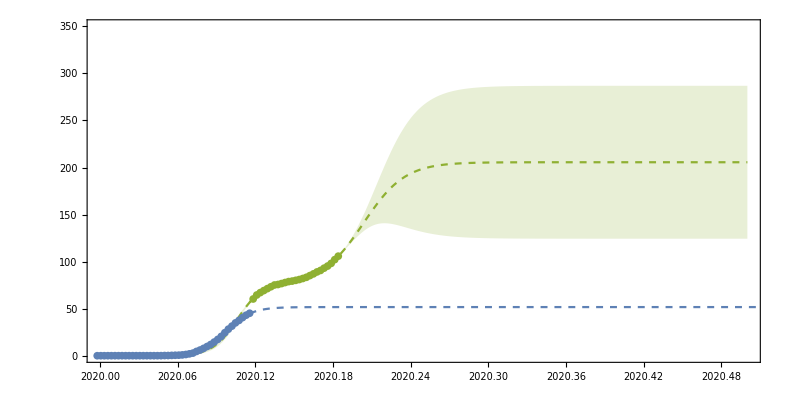

```mathematica
scale=0.001;
graphLimit=350000;
Show[
Plot[scale Normal[nlm],{t,2020,fitData[[-1,1]]},PlotRange->{{2020,2020.5},{0,scale*graphLimit}}],
Plot[scale Normal[nlm],{t,fitData[[-1,1]],2021},PlotRange->{0,scale*150000},PlotStyle->Dashed],
Plot[scale Normal[nlm2],{t,fitData[[-1,1]],fitData2[[-1,1]]},PlotRange->{0,scale*150000},PlotStyle->Directive[ColorData[97][3]]],
Plot[scale Normal[nlm2],{t,2020,2020.5},PlotRange->All,PlotStyle->Directive[Dashed,ColorData[97][3]]],
Plot[Evaluate[scale bands90],{t,2020,2020.5},PlotRange->All,PlotStyle->None,FillingStyle->Directive[Opacity[0.2],ColorData[97][3]],Filling->{1->{2}}],
ListPlot[{#[[1]],scale#[[2]]}&/@fitData,PlotStyle->PointSize[0.007]],
ListPlot[{#[[1]],scale#[[2]]}&/@Cases[accumulated,x_/;x[[1]]>2020.116],PlotStyle->Directive[PointSize[0.007],ColorData[97][3]]],
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False}]
```

```mathematica
1/365.24
```

0.00273793

```mathematica
Differences[totals[[All,1]]]
```

{0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793,0.00273793}

```mathematica
funcA=a0/(1+Exp[-(t-t0)/b0])/.nlm["BestFitParameters"];
funcAtotals=Table[{totals[[ii,1]],(funcA/.t->totals[[ii,1]])-(funcA/.t->totals[[ii-1,1]])},{ii,2,Length[totals]}];
```

```mathematica
func0=a0/(1+Exp[-(t-t0)/b0])/.nlm2["BestFitParameters"];
func0totals=Table[{totals[[ii,1]],(func0/.t->totals[[ii,1]])-(func0/.t->totals[[ii-1,1]])},{ii,2,Length[totals]}];
func1=a1/(1+Exp[-(t-t1)/b1])/.nlm2["BestFitParameters"];
func1totals=Table[{totals[[ii,1]],(func1/.t->totals[[ii,1]])-(func1/.t->totals[[ii-1,1]])},{ii,2,Length[totals]}];

func1atotals=Table[{tt,(func1/.t->tt)-(func1/.t->(tt-1/365.24))},{tt,totals[[-1,1]],2020.5,0.002}];
```

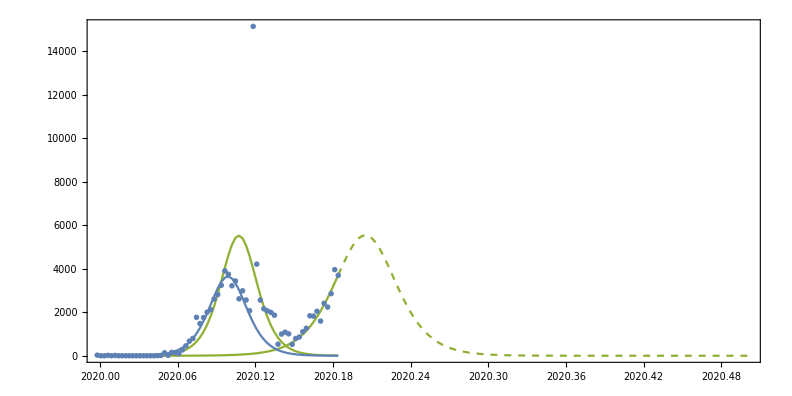

```mathematica
ListPlot[{totals,func0totals,func1totals,func1atotals,funcAtotals},PlotRange->{{2020,2020.5},All},Joined->{False,True,True,True,True},PlotStyle->{PointSize[0.005],ColorData[97][3],ColorData[97][3],Directive[Dashed,ColorData[97][3]],ColorData[97][1]},


ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False}]
```

```mathematica
totalsChina=Cases[data,x_/;x[[3]]=="China"][[All,{1,2}]];
```

```mathematica
dataNotChina=DeleteCases[data,x_/;x[[3]]=="China"];
totalsNotChina={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[dataNotChina[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
```

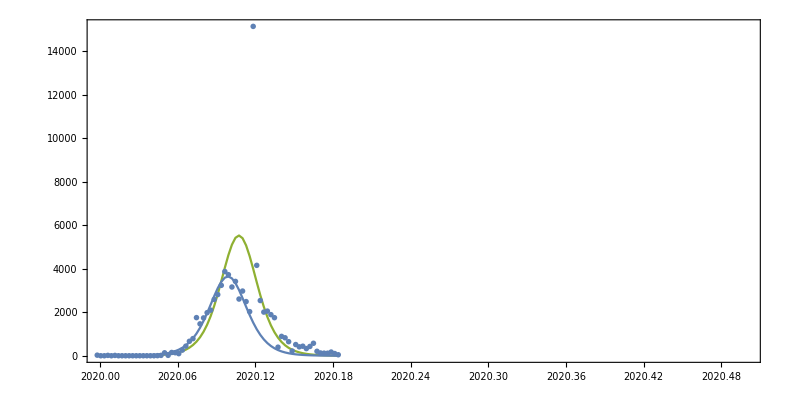

```mathematica
ListPlot[{totalsChina,func0totals,funcAtotals},PlotRange->{{2020,2020.5},All},Joined->{False,True,True},PlotStyle->{PointSize[0.005],ColorData[97][3],ColorData[97][1]},
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False}]
```

```mathematica
{a1,b1,t1}/.nlm2["BestFitParameters"]
```

{129360.,0.0159744,2020.2}

```mathematica
fitFunc=D[a1/(1+Exp[-(t-t1)/b1]),t]
nlmD=NonlinearModelFit[totalsNotChina,fitFunc,
{{a1,129359.8148811039},{b1,0.015974419434485302},{t1,2020.2034983782537}},
t]
```

(a1 ⅇ^((-t+t1)/b1))/(b1 (1+ⅇ^((-t+t1)/b1))^2)

FittedModel[(22665.6 ⅇ^(76.8442 («19»-t)))/((1+ⅇ^(«18» («19»-t)))^2)]

```mathematica
dataEU=Cases[data,x_/;x[[4]]=="EU"];
totalsEU={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[dataEU[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
```

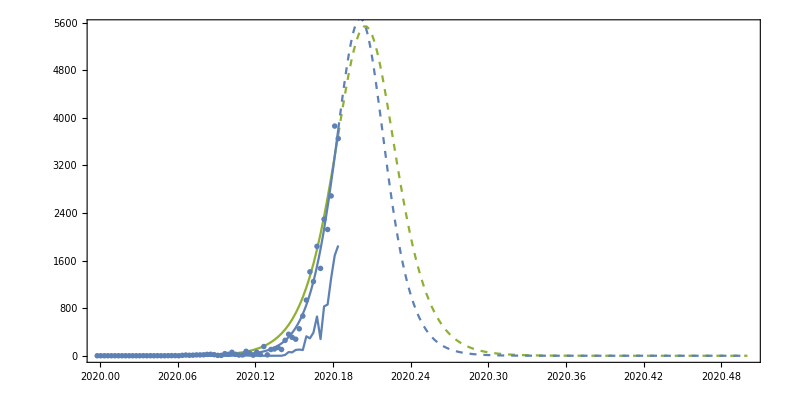

```mathematica
Show[
ListPlot[{totalsNotChina,func1totals,func1atotals,totalsEU},PlotRange->{{2020,2020.5},All},Joined->{False,True,True,True,True},PlotStyle->{PointSize[0.005],ColorData[97][3],Directive[Dashed,ColorData[97][3]],ColorData[97][1]},


ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False}],
Plot[Normal[nlmD],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]
```

```mathematica
totalsUSA=Cases[data,x_/;x[[3]]=="United States of America"][[All,{1,2}]];
```

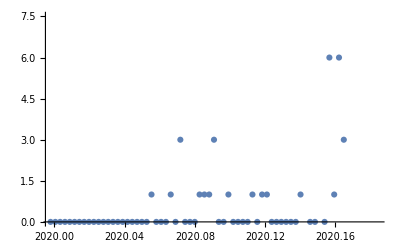

```mathematica
ListPlot[totalsUSA]
```

{{2020.18,1076.},{2020.18,1234.},{2020.18,591.},{2020.18,586.},{2020.17,835.},{2020.17,523.},{2020.17,385.},{2020.16,205.},{2020.16,143.},{2020.16,106.},{2020.16,44.},{2020.15,34.},{2020.15,18.},{2020.15,15.},{2020.15,10.},{2020.14,13.},{2020.14,3.},{2020.14,2.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.11,0.},{2020.11,0.},{2020.11,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.08,0.},{2020.08,0.},{2020.08,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.05,0.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

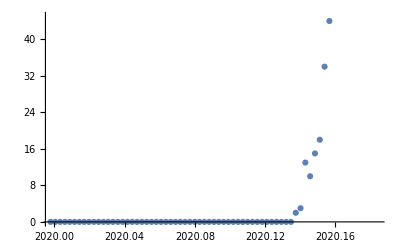

```mathematica
totalsIran=Cases[data,x_/;x[[3]]=="Iran"][[All,{1,2}]]
ListPlot[%]
```

## various countries

## China

```mathematica
totalsChina=Sort[Cases[data,x_/;x[[3]]=="China"][[All,{1,2}]]];
```

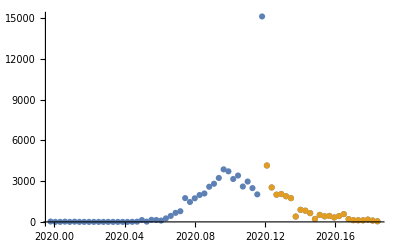

```mathematica
ListPlot[{totalsChina,Cases[totalsChina,x_/;x[[1]]>2020.119]},PlotRange->All]
```

FittedModel[(17989.1 ⅇ^(80.3171 («19»-t)))/((1+ⅇ^(«18» («19»-t)))^2)]

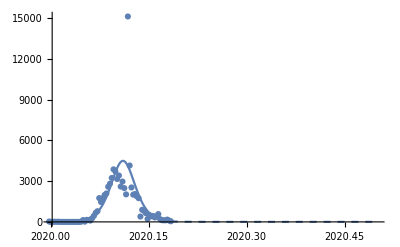

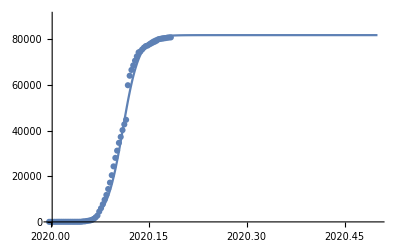

{{2020.12,64021.},{2020.12,66559.},{2020.13,68566.},{2020.13,70618.},{2020.13,72508.},{2020.13,74258.},{2020.14,74652.},{2020.14,75543.},{2020.14,76369.},{2020.15,77016.},{2020.15,77234.},{2020.15,77749.},{2020.15,78159.},{2020.16,78598.},{2020.16,78927.},{2020.16,79355.},{2020.16,79929.},{2020.17,80134.},{2020.17,80261.},{2020.17,80380.},{2020.18,80497.},{2020.18,80667.},{2020.18,80768.},{2020.18,80814.}}

FittedModel[80862.6/(1+ⅇ^(67.2714 («19»-t)))]

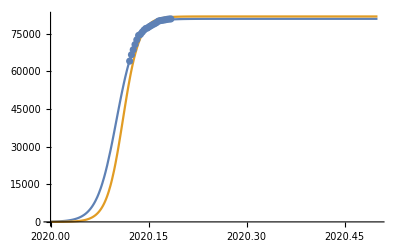

{(14893.6 ⅇ^(67.2714 (2020.1-tt)))/((1+ⅇ^(67.2714 (2020.1-tt)))^2),(17989.1 ⅇ^(80.3171 (2020.11-tt)))/((1+ⅇ^(80.3171 (2020.11-tt)))^2)}

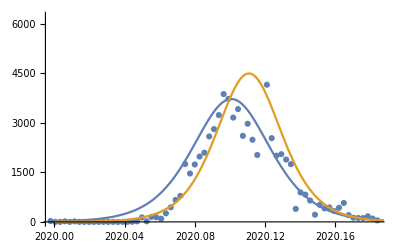

80862.6/(1+ⅇ^(67.2714 (2020.1-t)))

```mathematica
fitDataD0=totalsChina;
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

temp=Cases[accumulatedD0,x_/;x[[1]]>2020.119]
nlmChina=NonlinearModelFit[temp,aD/(1+Exp[-(t-tD)/bD]),
{{aD,50000},{bD,0.01},{tD,2020.15}},t]
Show[Plot[{Normal[nlmChina],tempfunc},{t,2020,2020.5}],ListPlot[temp]]
tempD=Evaluate[(1/365.24){D[Normal[nlmChina],t]/.t->tt,D[tempfunc,t]/.t->tt}]
Show[ListPlot[totalsChina],Plot[tempD,{tt,2020,2020.5},PlotRange->All]]


funcChina=Normal[nlmChina]
```

## Korea

{{2020.18,367.},{2020.18,483.},{2020.18,518.},{2020.18,438.},{2020.17,516.},{2020.17,600.},{2020.17,686.},{2020.16,595.},{2020.16,909.},{2020.16,427.},{2020.16,449.},{2020.15,254.},{2020.15,130.},{2020.15,161.},{2020.15,256.},{2020.14,190.},{2020.14,75.},{2020.14,34.},{2020.13,15.},{2020.13,1.},{2020.13,1.},{2020.13,1.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.11,1.},{2020.11,2.},{2020.11,1.},{2020.1,0.},{2020.1,1.},{2020.1,5.},{2020.1,2.},{2020.09,1.},{2020.09,0.},{2020.09,3.},{2020.09,5.},{2020.08,3.},{2020.08,0.},{2020.08,0.},{2020.07,0.},{2020.07,1.},{2020.07,1.},{2020.07,0.},{2020.06,1.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.05,1.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

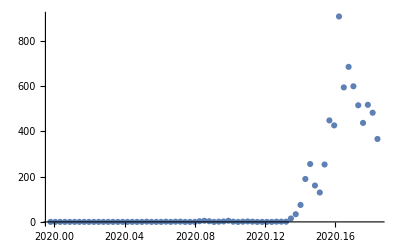

```mathematica
totalsKorea=Cases[data,x_/;x[[3]]=="South Korea"][[All,{1,2}]]
ListPlot[%,PlotRange->All]
```

FittedModel[(2673.96 ⅇ^(119.965 («19»-t)))/((1+ⅇ^(«19» («19»-t)))^2)]

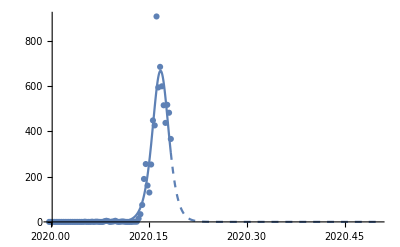

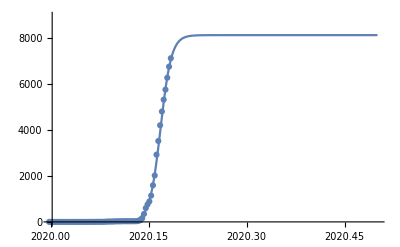

```mathematica
fitDataD0=Sort[totalsKorea];
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcKorea=tempfunc;
```

## Japan

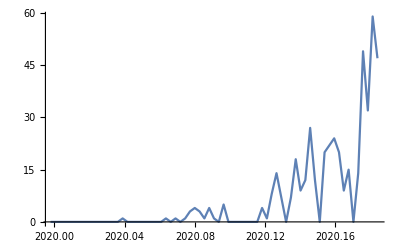

```mathematica
totalsJapan=Cases[data,x_/;x[[3]]=="Japan"][[All,{1,2}]];
(*totalsJapan={#[[1,1]],Total[#[[All,2]]]}&/@(Split[Sort[totalsJapan],#1[[1]]==#2[[1]]&]);*)
ListPlot[%,PlotRange->All,Joined->True]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[(362540. ⅇ^(41.0427 («18»-t)))/((1+ⅇ^(«18» («18»-t)))^2)]

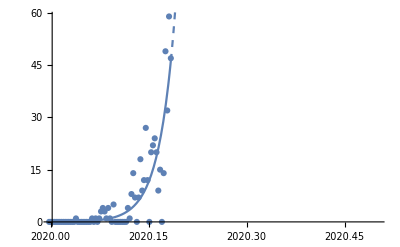

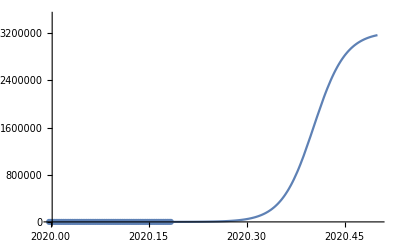

```mathematica
fitDataD0=Sort[totalsJapan];
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcJapan=tempfunc;
```

## Iran

{{2020.18,1076.},{2020.18,1234.},{2020.18,591.},{2020.18,586.},{2020.17,835.},{2020.17,523.},{2020.17,385.},{2020.16,205.},{2020.16,143.},{2020.16,106.},{2020.16,44.},{2020.15,34.},{2020.15,18.},{2020.15,15.},{2020.15,10.},{2020.14,13.},{2020.14,3.},{2020.14,2.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.11,0.},{2020.11,0.},{2020.11,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.08,0.},{2020.08,0.},{2020.08,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.05,0.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

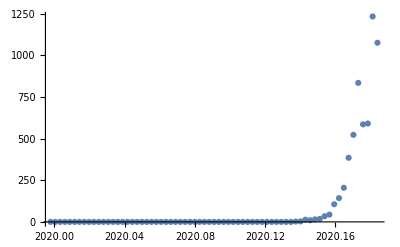

```mathematica
totalsIran=Cases[data,x_/;x[[3]]=="Iran"][[All,{1,2}]]
ListPlot[%,PlotRange->All]
```

FittedModel[(4601.71 ⅇ^(125.426 («19»-t)))/((1+ⅇ^(«19» («19»-t)))^2)]

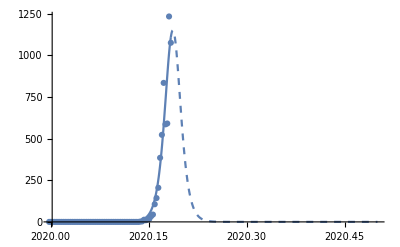

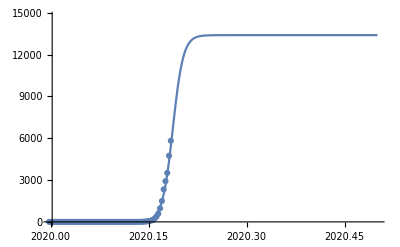

```mathematica
fitDataD0=Sort[totalsIran];
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcIran=tempfunc;
```

## France

{{2020.18,103.},{2020.18,190.},{2020.18,138.},{2020.18,73.},{2020.17,34.},{2020.17,48.},{2020.17,30.},{2020.16,43.},{2020.16,19.},{2020.16,21.},{2020.16,3.},{2020.15,2.},{2020.15,0.},{2020.15,0.},{2020.15,0.},{2020.14,0.},{2020.14,0.},{2020.14,0.},{2020.13,0.},{2020.13,0.},{2020.13,1.},{2020.13,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.11,0.},{2020.11,0.},{2020.11,0.},{2020.1,5.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.08,1.},{2020.08,1.},{2020.08,1.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.07,3.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.05,0.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

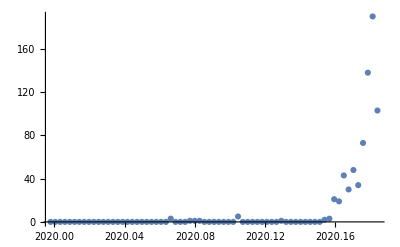

```mathematica
totalsFrance=Cases[data,x_/;x[[3]]=="France"][[All,{1,2}]]
ListPlot[%,PlotRange->All]
```

FittedModel[(685.39 ⅇ^(371.207 («19»-t)))/((1+ⅇ^(«18» («19»-t)))^2)]

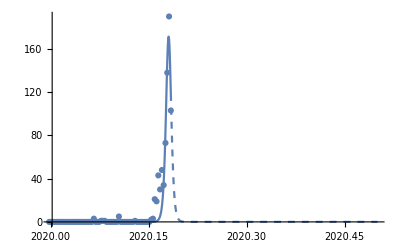

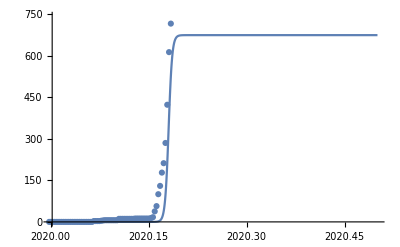

```mathematica
fitDataD0=Sort[totalsFrance];
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcFrance=tempfunc;
```

## Italy

{{2020.18,1247.},{2020.18,778.},{2020.18,769.},{2020.18,587.},{2020.17,667.},{2020.17,146.},{2020.17,561.},{2020.16,240.},{2020.16,238.},{2020.16,250.},{2020.16,78.},{2020.15,93.},{2020.15,97.},{2020.15,53.},{2020.15,62.},{2020.14,14.},{2020.14,0.},{2020.14,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.12,0.},{2020.11,0.},{2020.11,0.},{2020.11,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.1,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.09,0.},{2020.08,3.},{2020.08,0.},{2020.08,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.07,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.05,0.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

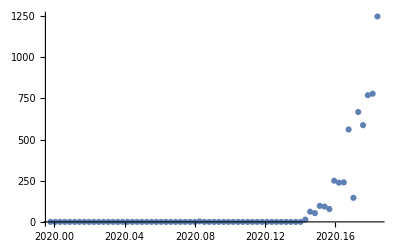

```mathematica
totalsItaly=Cases[data,x_/;x[[3]]=="Italy"][[All,{1,2}]]
ListPlot[%,PlotRange->All]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[(786275. ⅇ^(77.4488 («19»-t)))/((1+ⅇ^(«18» («19»-t)))^2)]

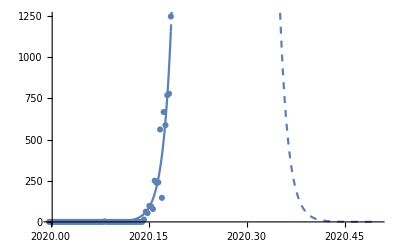

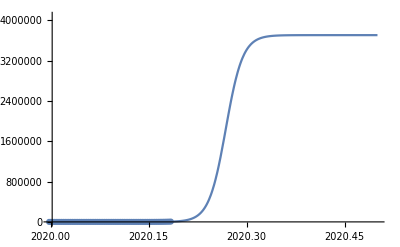

```mathematica
fitDataD0=Sort[totalsItaly];
fitFuncD0=D[aD/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{{aD,50000},{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 aD/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcItaly=tempfunc;
```

## USA (fit cumulative)

{{2020.18,95.},{2020.18,105.},{2020.18,74.},{2020.18,34.},{2020.17,22.},{2020.17,14.},{2020.17,20.},{2020.16,3.},{2020.16,6.},{2020.16,1.},{2020.16,6.},{2020.15,0.},{2020.15,18.},{2020.15,0.},{2020.15,0.},{2020.14,19.},{2020.14,1.},{2020.14,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.13,0.},{2020.12,0.},{2020.12,1.},{2020.12,1.},{2020.12,0.},{2020.11,1.},{2020.11,0.},{2020.11,0.},{2020.1,0.},{2020.1,0.},{2020.1,1.},{2020.1,0.},{2020.09,0.},{2020.09,3.},{2020.09,1.},{2020.09,1.},{2020.08,1.},{2020.08,0.},{2020.08,0.},{2020.07,0.},{2020.07,3.},{2020.07,0.},{2020.07,1.},{2020.06,0.},{2020.06,0.},{2020.06,0.},{2020.06,1.},{2020.05,0.},{2020.05,0.},{2020.05,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.04,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.03,0.},{2020.02,0.},{2020.02,0.},{2020.02,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.01,0.},{2020.,0.},{2020.,0.},{2020.,0.}}

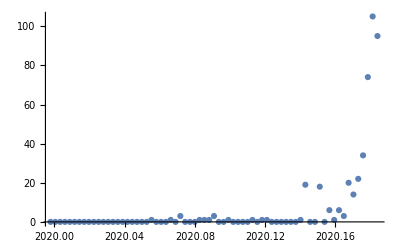

```mathematica
totalsUSA=Cases[data,x_/;x[[3]]=="United States of America"][[All,{1,2}]]
ListPlot[%,PlotRange->All]
```

```mathematica
(* estimate saturation using China *)
funcChina/.t->2020.5
%/(1.386*10^9)
caseSatUS=327.2*10^6*%


(* estimate saturation using Korea *)
funcKorea/.t->2020.5
%/(51.47*10^6)
caseSatUS=327.2*10^6*%
```

80862.6

0.0000583424

19089.6

8141.

0.00015817

51753.2

FittedModel[51753.2/(1+ⅇ^(91.6403 (2020.24-t)))]

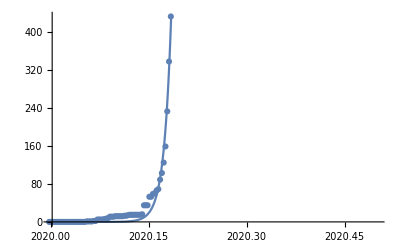

51753.2/(1+ⅇ^(91.6403 (2020.24-t)))

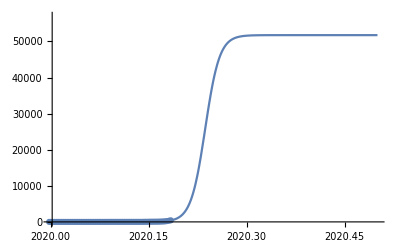

```mathematica
fitDataD0=Sort[totalsUSA];
accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];
fitFuncD0=caseSatUS/(1+Exp[-(t-tD)/bD]);
nlmD0=NonlinearModelFit[accumulatedD0,fitFuncD0,
{{bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

tempfunc=Normal[nlmD0]
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcUSA=tempfunc;
```

## EU

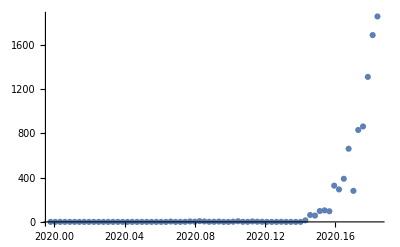

```mathematica
dataEU=Cases[data,x_/;x[[4]]=="EU"];
totalsEU={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[dataEU[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
ListPlot[%,PlotRange->All]
```

```mathematica
(* estimate saturation using Korea *)
funcKorea/.t->2030.5
%/(51.47*10^6)
caseSatEU=(512.4*10^6*%)/365.24
```

8141.

0.00015817

221.899

FittedModel[(21640. ⅇ^(97.522 («19»-t)))/((1+ⅇ^(«18» («19»-t)))^2)]

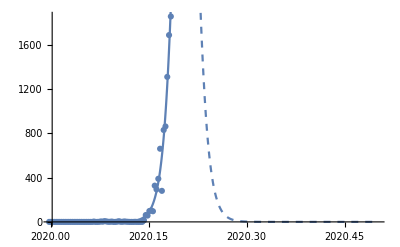

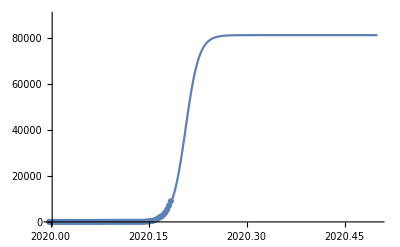

```mathematica
fitDataD0=Sort[totalsEU];
fitFuncD0=D[caseSatEU/(1+Exp[-(t-tD)/bD]),t];
nlmD0=NonlinearModelFit[fitDataD0,fitFuncD0,
{(*{aD,50000},*){bD,0.01},{tD,2020.15}},
t]
Show[ListPlot[fitDataD0,PlotRange->{{2020,2020.5},All}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

tempfunc=365.24 caseSatEU/(1+Exp[-(t-tD)/bD])/.nlmD0["BestFitParameters"];
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcEU=tempfunc;
```

## Others (fit cumulative)

```mathematica
others=DeleteCases[data,x_/;x[[3]]=="China"||x[[3]]=="South Korea"||x[[4]]=="EU"||x[[3]]=="Iran"][[All,{1,2}]];
totalsOthers={#[[1,1]],Total[#[[All,2]]]}&/@Split[Sort[others[[All,{1,2}]]],#1[[1]]==#2[[1]]&];
```

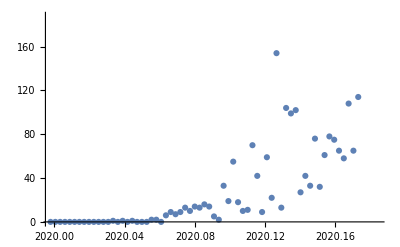

```mathematica
ListPlot[totalsOthers]
```

FittedModel[1764.3/(1+ⅇ^(56.8068 («19»-t)))+2388.53/(1+ⅇ^(239.781 («19»-t)))]

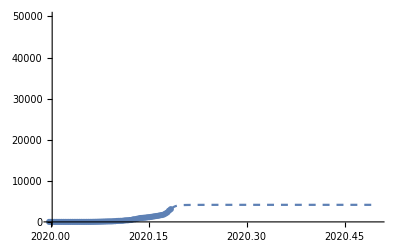

1764.3/(1+ⅇ^(56.8068 (2020.14-t)))+2388.53/(1+ⅇ^(239.781 (2020.18-t)))

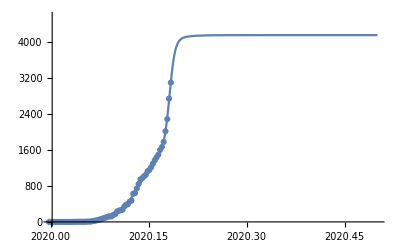

```mathematica
fitDataD0=Sort[totalsOthers];
accumulatedD0=Transpose[{fitDataD0[[All,1]],Accumulate[fitDataD0[[All,2]]]}];

fitFuncD0=aD/(1+Exp[-(t-tD)/bD])+aD1/(1+Exp[-(t-tD1)/bD1]);
nlmD0=NonlinearModelFit[accumulatedD0,fitFuncD0,
{
{aD,150000.1},{bD,0.01},{tD,2020.1},
{aD1,150000.1},{bD1,0.01},{tD1,2020.2}
},
t,Method->Automatic]

Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,50000}}],
Plot[Normal[nlmD0],{t,2020,totals[[-1,1]]},PlotRange->All],
Plot[Normal[nlmD0],{t,totals[[-1,1]],2020.5},PlotRange->All,PlotStyle->Dashed]]

tempfunc=Normal[nlmD0]
Show[ListPlot[accumulatedD0,PlotRange->{{2020,2020.5},{0,1.1tempfunc/.t->2020.5}}],Plot[tempfunc,{t,2020,2020.5}]]

funcOthers=tempfunc;
```

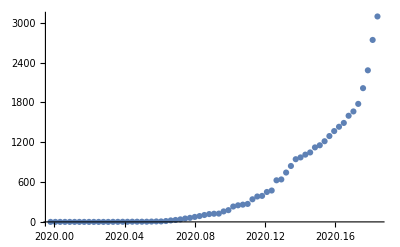

```mathematica
ListPlot[accumulatedD0]
```

```mathematica
nlmOthers=nlmD0
```

FittedModel[1764.3/(1+ⅇ^(56.8068 («19»-t)))+2388.53/(1+ⅇ^(239.781 («19»-t)))]

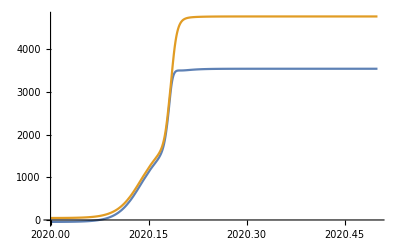

```mathematica
nlmOthers["SinglePredictionBands"];
Plot[%,{t,2020,2020.5}]
```

## summing up (others)

```mathematica
endYear=2020.4;
scale=0.001;
```

```mathematica
monthList={"J","F","M","A","M","J","J","A","S","O","N","D"};
labels=Table[{1900+FromDate[{2020,ii,1,0,0,0}]/(365.24*3600*24),monthList[[ii]]},{ii,1,12}];
```

```mathematica
{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsOthers,totalsUSA,totalsFrance,totalsItaly}=Sort/@{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsOthers,totalsUSA,totalsFrance,totalsItaly};
```

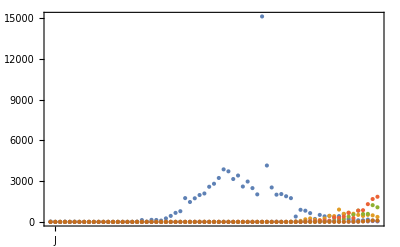

```mathematica
ListPlot[{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsUSA},PlotRange->All,Frame->True,FrameTicks->{{Automatic,Automatic},{labels,Automatic}}]
```

```mathematica
accumulatedChina=Transpose[{totalsChina[[All,1]],scale Accumulate[totalsChina[[All,2]]]}];
accumulatedKorea=Transpose[{totalsKorea[[All,1]],scale Accumulate[totalsKorea[[All,2]]]}];
accumulatedIran=Transpose[{totalsIran[[All,1]],scale Accumulate[totalsIran[[All,2]]]}];
accumulatedEU=Transpose[{totalsEU[[All,1]],scale Accumulate[totalsEU[[All,2]]]}];
accumulatedUSA=Transpose[{totalsUSA[[All,1]],scale Accumulate[totalsUSA[[All,2]]]}];
accumulatedOthers=Transpose[{totalsOthers[[All,1]],scale Accumulate[totalsOthers[[All,2]]]}];

accumulatedFrance=Transpose[{totalsFrance[[All,1]],scale Accumulate[totalsFrance[[All,2]]]}];
accumulatedItaly=Transpose[{totalsItaly[[All,1]],scale Accumulate[totalsItaly[[All,2]]]}];
accumulatedJapan=Transpose[{totalsJapan[[All,1]],scale Accumulate[totalsJapan[[All,2]]]}];
```

{80.8626/(1+ⅇ^(67.2714 (2020.1-t))),8.141/(1+ⅇ^(119.965 (2020.17-t))),13.4002/(1+ⅇ^(125.426 (2020.19-t))),81.0463/(1+ⅇ^(97.522 (2020.21-t))),0.001 (1764.3/(1+ⅇ^(56.8068 (2020.14-t)))+2388.53/(1+ⅇ^(239.781 (2020.18-t))))}

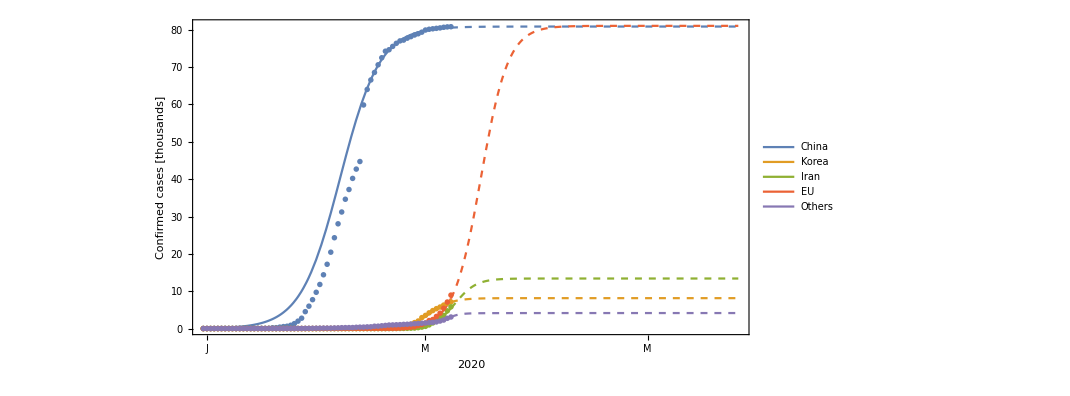

```mathematica
cums=scale{funcChina,funcKorea,funcIran,funcEU,funcOthers}
p1=Show[
Plot[cums,{t,2020,totals[[-1,1]]},PlotRange->All,PlotLegends->{"China","Korea","Iran","EU","Others"}],
Plot[cums,{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Dashed],
ListPlot[{accumulatedChina,accumulatedKorea,accumulatedIran,accumulatedEU,accumulatedOthers},PlotStyle->PointSize[0.005]],
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"}]
```

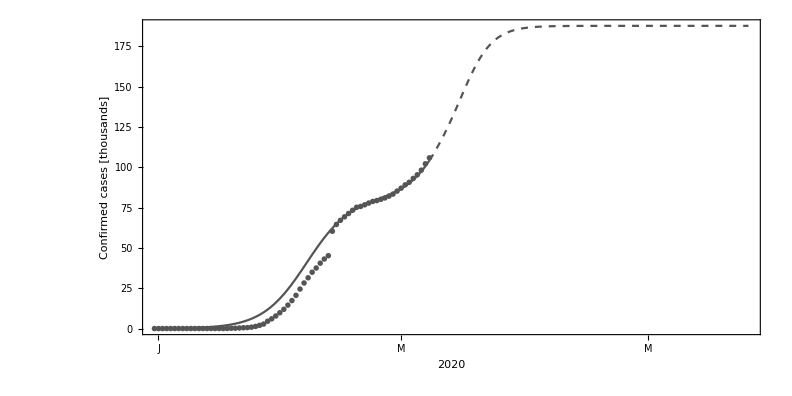

```mathematica
p0=Show[
Plot[Total[cums],{t,2020,totals[[-1,1]]},PlotRange->All,PlotStyle->Lighter[Black]],
Plot[Total[cums],{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Directive[Dashed,Lighter[Black]]],
ListPlot[{#[[1]],scale#[[2]]}&/@accumulated,PlotStyle->Directive[PointSize[0.005],Lighter[Black]]],
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"}]
```

{(14893.6 ⅇ^(67.2714 (2020.1-t)))/((1+ⅇ^(67.2714 (2020.1-t)))^2),(2673.96 ⅇ^(119.965 (2020.17-t)))/((1+ⅇ^(119.965 (2020.17-t)))^2),(4601.71 ⅇ^(125.426 (2020.19-t)))/((1+ⅇ^(125.426 (2020.19-t)))^2),(21640. ⅇ^(97.522 (2020.21-t)))/((1+ⅇ^(97.522 (2020.21-t)))^2),0.00273793 ((100225. ⅇ^(56.8068 (2020.14-t)))/((1+ⅇ^(56.8068 (2020.14-t)))^2)+(572723. ⅇ^(239.781 (2020.18-t)))/((1+ⅇ^(239.781 (2020.18-t)))^2))}

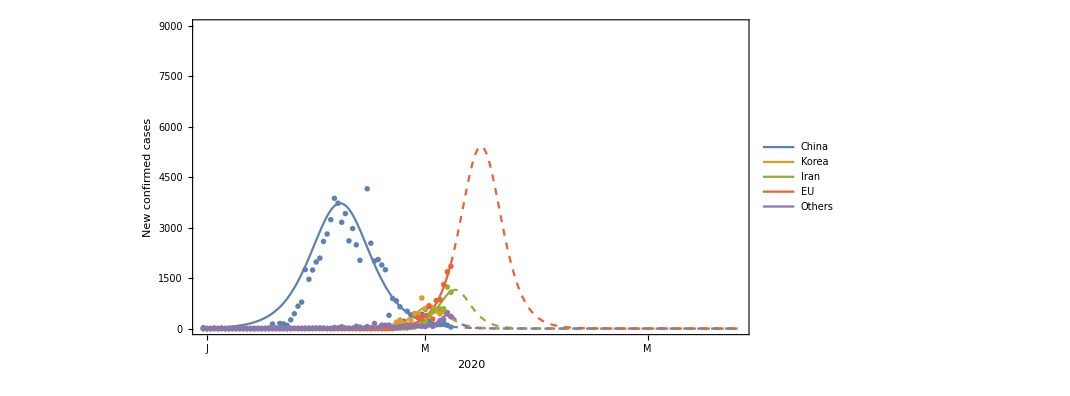

```mathematica
derivatives=(1/365.24){D[funcChina,t],D[funcKorea,t],D[funcIran,t],D[funcEU,t],D[funcOthers,t]}
Show[
Plot[derivatives,{t,2020,totals[[-1,1]]},PlotRange->All,PlotLegends->{"China","Korea","Iran","EU","Others"}],
Plot[derivatives,{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Dashed],
ListPlot[{totalsChina,totalsKorea,totalsIran,totalsEU,totalsOthers},PlotRange->Automatic,PlotStyle->PointSize[0.005]],

ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},PlotRange->{0,9000},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nNew confirmed cases"}]
```

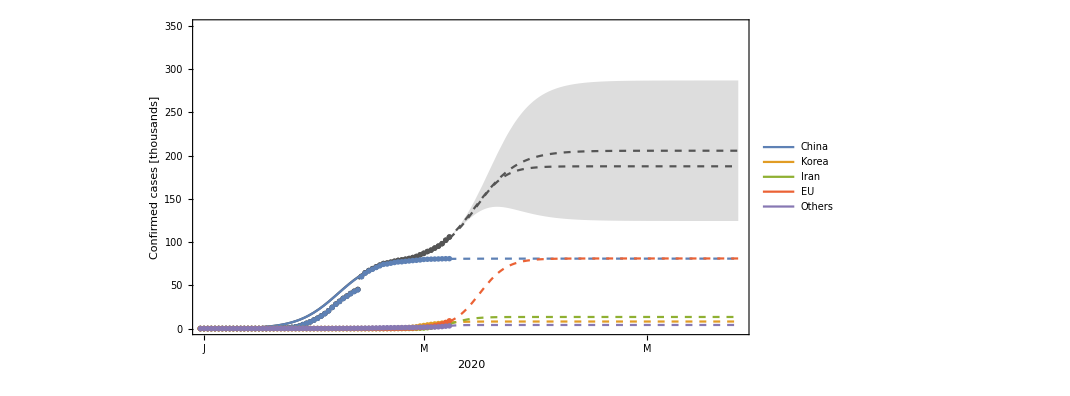

```mathematica
graphLimit=350000;
Show[
Plot[scale Normal[nlm2],{t,2020.116,endYear},PlotRange->{{2020,endYear},{0,scale*graphLimit}},PlotStyle->Directive[Dashed,Lighter[Black]]],
Plot[scale Normal[nlm2],{t,2020.116,totals[[-1,1]]},PlotStyle->Directive[Lighter[Black]]],
Plot[Evaluate[scale bands90],{t,2020.116,endYear},PlotRange->All,PlotStyle->None,FillingStyle->Directive[Opacity[0.2],Lighter[Black]],Filling->{1->{2}}],
ListPlot[{#[[1]],scale#[[2]]}&/@accumulated,PlotStyle->Directive[PointSize[0.005],Lighter[Black]],
PlotStyle->Directive[PointSize[0.007],ColorData[97][3]]],
p0,p1,
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"}]
```

## summing up (USA)

```mathematica
endYear=2020.4;
scale=0.001;
```

```mathematica
monthList={"J","F","M","A","M","J","J","A","S","O","N","D"};
labels=Table[{1900+FromDate[{2020,ii,1,0,0,0}]/(365.24*3600*24),monthList[[ii]]},{ii,1,12}];
```

```mathematica
{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsUSA}=Sort/@{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsUSA};
```

```mathematica
ListPlot[{totalsChina,totalsKorea,totalsIran,totalsEU,totalsJapan,totalsUSA},PlotRange->All,Frame->True,FrameTicks->{{Automatic,Automatic},{labels,Automatic}}]
```

-Graphics-

```mathematica
accumulatedChina=Transpose[{totalsChina[[All,1]],scale Accumulate[totalsChina[[All,2]]]}];
accumulatedKorea=Transpose[{totalsKorea[[All,1]],scale Accumulate[totalsKorea[[All,2]]]}];
accumulatedIran=Transpose[{totalsIran[[All,1]],scale Accumulate[totalsIran[[All,2]]]}];
accumulatedEU=Transpose[{totalsEU[[All,1]],scale Accumulate[totalsEU[[All,2]]]}];
accumulatedUSA=Transpose[{totalsUSA[[All,1]],scale Accumulate[totalsUSA[[All,2]]]}];
accumulatedOthers=Transpose[{totalsOthers[[All,1]],scale Accumulate[totalsOthers[[All,2]]]}];
```

```mathematica
(* estimated EU saturation based on China *)
80.86256857818246*(0.5124/1.386)

(* function fit is 51.183911888429016 *)
```

29.8946

```mathematica
(* estimated EU saturation based on korea *)
8.141004638776039*(0.5124/0.05747)
```

72.5848

```mathematica
(* estimated Korea saturation based on China *)
80.86256857818246*(0.0575/1.386)

(* actual is 8.141004638776039 *)
```

3.35469

{80.8626/(1+ⅇ^(67.2714 (2020.1-t))),8.141/(1+ⅇ^(119.965 (2020.17-t))),13.4002/(1+ⅇ^(125.426 (2020.19-t))),81.0463/(1+ⅇ^(97.522 (2020.21-t))),51.7532/(1+ⅇ^(91.6403 (2020.24-t)))}

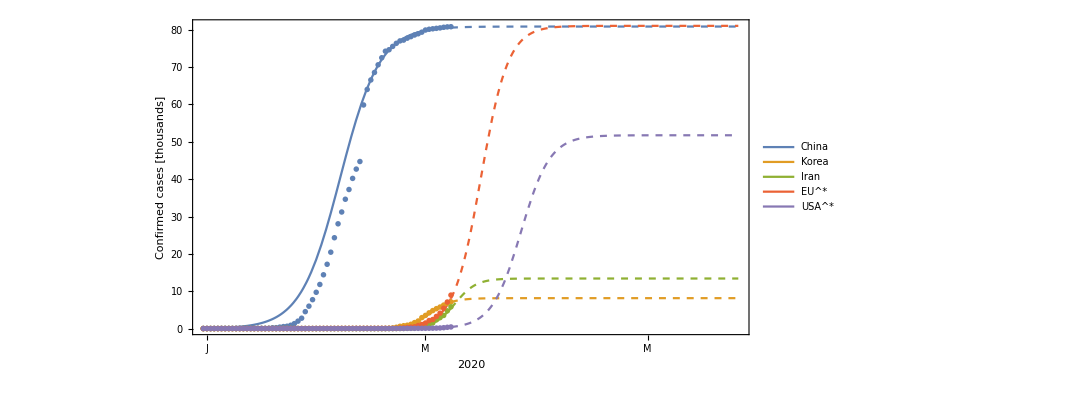

```mathematica
cums=scale{funcChina,funcKorea,funcIran,funcEU,funcUSA}
p1=Show[
Plot[cums,{t,2020,totals[[-1,1]]},PlotRange->All,PlotLegends->{"China","Korea","Iran","EU^*","USA^*"}],
Plot[cums,{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Dashed],
ListPlot[{accumulatedChina,accumulatedKorea,accumulatedIran,accumulatedEU,accumulatedUSA},PlotStyle->PointSize[0.005]],
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"}]
```

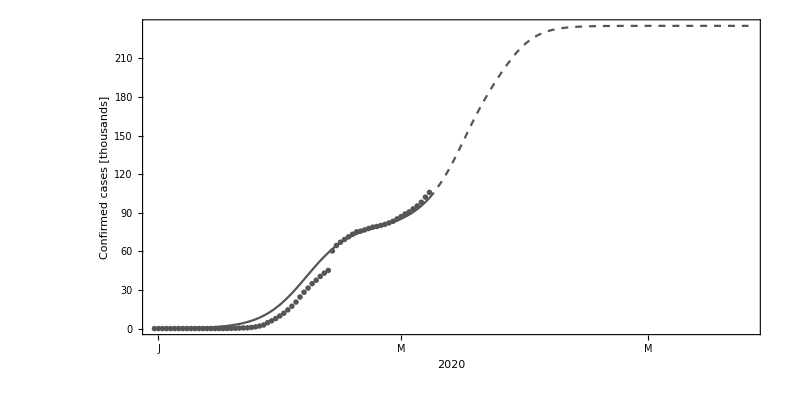

```mathematica
p0=Show[
Plot[Total[cums],{t,2020,totals[[-1,1]]},PlotRange->All,PlotStyle->Lighter[Black]],
Plot[Total[cums],{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Directive[Dashed,Lighter[Black]]],
ListPlot[{#[[1]],scale#[[2]]}&/@accumulated,PlotStyle->Directive[PointSize[0.005],Lighter[Black]]],
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"}]
```

{(14893.6 ⅇ^(67.2714 (2020.1-t)))/((1+ⅇ^(67.2714 (2020.1-t)))^2),(2673.96 ⅇ^(119.965 (2020.17-t)))/((1+ⅇ^(119.965 (2020.17-t)))^2),(4601.71 ⅇ^(125.426 (2020.19-t)))/((1+ⅇ^(125.426 (2020.19-t)))^2),(21640. ⅇ^(97.522 (2020.21-t)))/((1+ⅇ^(97.522 (2020.21-t)))^2),(12985.1 ⅇ^(91.6403 (2020.24-t)))/((1+ⅇ^(91.6403 (2020.24-t)))^2)}

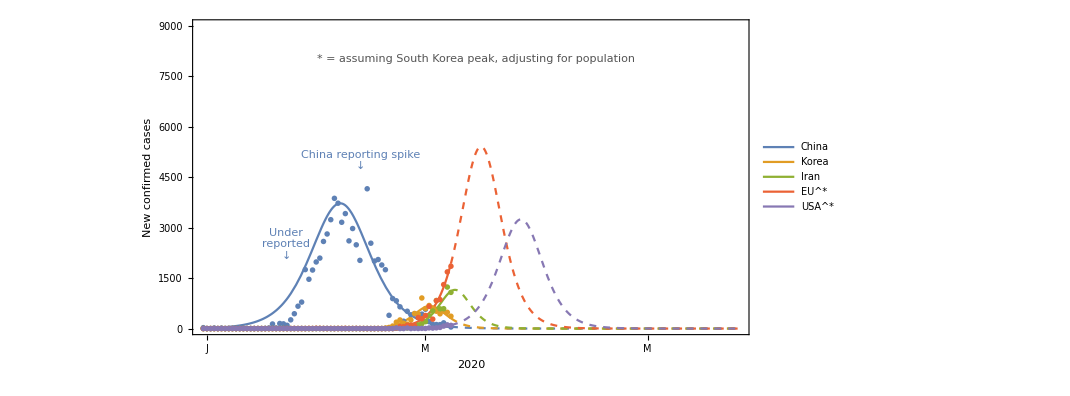

```mathematica
derivatives=(1/365.24){D[funcChina,t],D[funcKorea,t],D[funcIran,t],D[funcEU,t],D[funcUSA,t]}
Show[
Plot[derivatives,{t,2020,totals[[-1,1]]},PlotRange->All,PlotLegends->{"China","Korea","Iran","EU^*","USA^*"}],
Plot[derivatives,{t,totals[[-1,1]],endYear},PlotRange->All,PlotStyle->Dashed],
ListPlot[{totalsChina,totalsKorea,totalsIran,totalsEU,totalsUSA},PlotRange->Automatic,PlotStyle->PointSize[0.005]],

ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},PlotRange->{0,9000},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nNew confirmed cases"},
Epilog->{Lighter[Black],Text["* = assuming South Korea peak, adjusting for population",{2020+1/12,8000},{-1,0}],ColorData[97][1],Text["China reporting spike\n↓",{2020.116,5000}],
Text["Under\nreported\n↓",{2020.06,2500}]}]
```

```mathematica
(14893.591987011561 ⅇ^(67.27136712305474 (2020.1007739265672-t)))/((1+ⅇ^(67.27136712305474 (2020.1007739265672-t)))^2)/.t->2019+11/12+(15/31)/12
```

0.937975

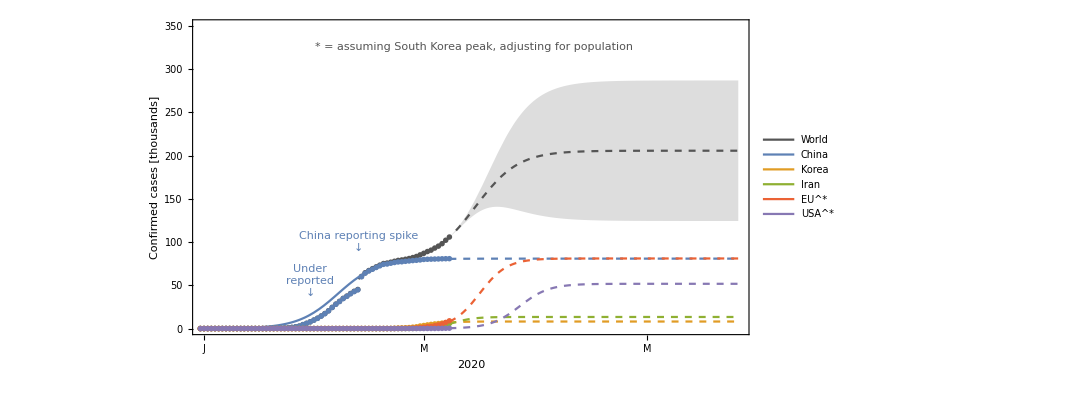

```mathematica
graphLimit=350000;
Show[
Plot[scale Normal[nlm2],{t,2020.116,endYear},PlotRange->{{2020,endYear},{0,scale*graphLimit}},PlotStyle->Directive[Dashed,Lighter[Black]]],
Plot[scale Normal[nlm2],{t,2020.116,totals[[-1,1]]},PlotStyle->Directive[Lighter[Black]],PlotLegends->{"World"}],
Plot[Evaluate[scale bands90],{t,2020.116,endYear},PlotRange->All,PlotStyle->None,FillingStyle->Directive[Opacity[0.2],Lighter[Black]],Filling->{1->{2}}],
ListPlot[{#[[1]],scale#[[2]]}&/@accumulated,PlotStyle->Directive[PointSize[0.005],Lighter[Black]],
PlotStyle->Directive[PointSize[0.007],ColorData[97][3]]],
p1,
ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"},

Epilog->{Lighter[Black],Text["* = assuming South Korea peak, adjusting for population",{2020+1/12,325},{-1,0}],ColorData[97][1],Text["China reporting spike\n↓",{2020.116,100}],Text["Under\nreported\n↓",{2020.08,55}]}]
```

## various countries

```mathematica
trip=(totalsItaly[[-1,1]]-14/365.24)
```

2020.15

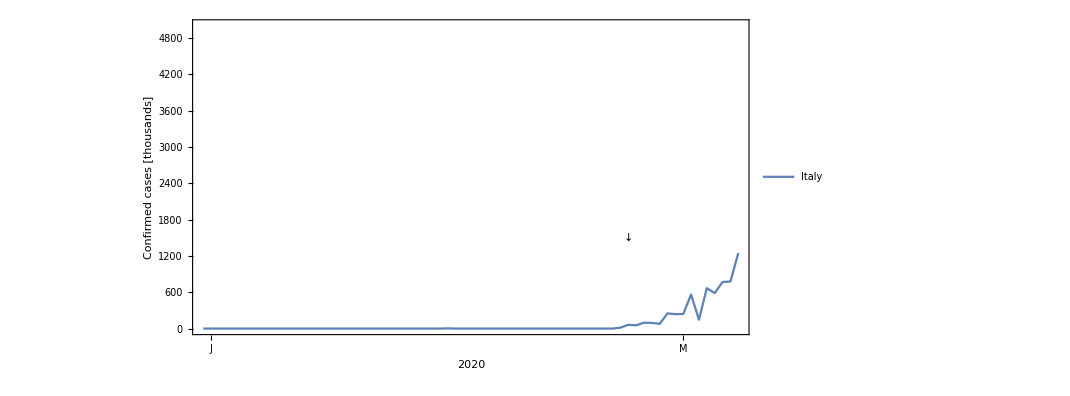

```mathematica
ListPlot[{totalsItaly},Joined->True,PlotRange->{0,5000},ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"},PlotLegends->{"Italy"},Epilog->{Text["↓",{trip,1500}]}]
```

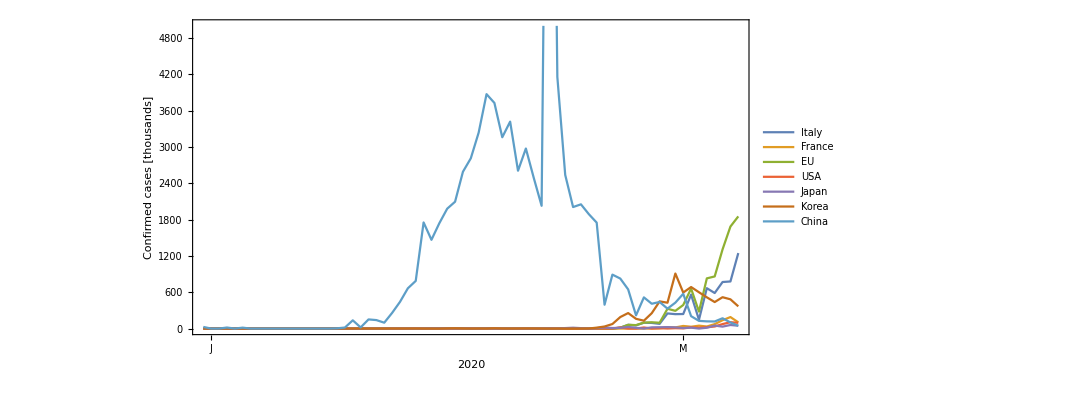

```mathematica
ListPlot[{totalsItaly,totalsFrance,totalsEU,totalsUSA,totalsJapan,totalsKorea,totalsChina},Joined->True,PlotRange->{0,5000},ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"},PlotLegends->{"Italy","France","EU","USA","Japan","Korea","China"}]
```

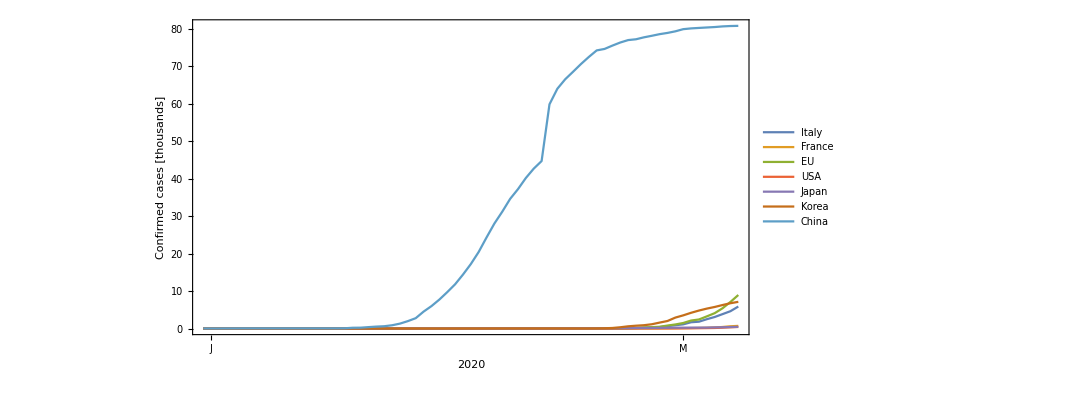

```mathematica
ListPlot[{accumulatedItaly,accumulatedFrance,accumulatedEU,accumulatedUSA,accumulatedJapan,accumulatedKorea,accumulatedChina},Joined->True,PlotRange->All,ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,False,False},FrameTicks->{{Automatic,Automatic},{labels,Automatic}},FrameLabel->{"2020\n","\nConfirmed cases [thousands]"},PlotLegends->{"Italy","France","EU","USA","Japan","Korea","China"}]
```

## math stuff

```mathematica
1/366.
```

0.00273224

```mathematica
mathData={(#[[1]]-2020+0.00219035)*365.24,#[[2]]}&/@totalsKorea
```

{{3.434×10^-6,0.},{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,1.},{21.,0.},{22.,0.},{23.,0.},{24.,1.},{25.,0.},{26.,1.},{27.,1.},{28.,0.},{29.,0.},{30.,0.},{31.,3.},{32.,5.},{33.,3.},{34.,0.},{35.,1.},{36.,2.},{37.,5.},{38.,1.},{39.,0.},{40.,1.},{41.,2.},{42.,1.},{43.,0.},{44.,0.},{45.,0.},{46.,0.},{47.,1.},{48.,1.},{49.,1.},{50.,15.},{51.,34.},{52.,75.},{53.,190.},{54.,256.},{55.,161.},{56.,130.},{57.,254.},{58.,449.},{59.,427.},{60.,909.},{61.,595.},{62.,686.},{63.,600.},{64.,516.},{65.,438.},{66.,518.},{67.,483.},{68.,367.}}

```mathematica
1/(119.96536665808414)
%*365.24
```

0.00833574

3.04455

```mathematica
funcKorea
```

8141./(1+ⅇ^(119.965 (2020.17-t)))

```mathematica
params={a0->8141.0046387760385,b0->3.0,t0->0.17*365.24}
```

{a0→8141.,b0→3.,t0→62.0908}

```mathematica
a0/(1+Exp[-(t-t0)/b0])
```

a0/(1+ⅇ^((-t+t0)/b0))

```mathematica
(Series[a0/(1+y),{y,∞,1}])
Normal[%]/.y->1/y
%/.(y->Exp[(t-t0)/b0])//Simplify
firstOrder=%/.params
```

a0/y+O[1/y]^2

a0 y

a0 ⅇ^((t-t0)/b0)

8141. ⅇ^(0.333333 (-62.0908+t))

```mathematica
(Series[a0/(1+y),{y,∞,2}])
Normal[%]/.y->1/y
%/.(y->Exp[(t-t0)/b0])//Simplify
secondOrder=%/.params
```

a0/y-a0/y^2+O[1/y]^3

a0 y-a0 y^2

a0 ⅇ^((t-t0)/b0)-a0 ⅇ^((2 (t-t0))/b0)

8141. ⅇ^(0.333333 (-62.0908+t))-8141. ⅇ^(0.666667 (-62.0908+t))

```mathematica
test=a0/(1+Exp[-(t-t0)/b0])/.params
```

8141./(1+ⅇ^(0.333333 (62.0908-t)))

```mathematica
der=D[test,t]
```

(2713.67 ⅇ^(0.333333 (62.0908-t)))/((1+ⅇ^(0.333333 (62.0908-t)))^2)

```mathematica
width=(2Log[3+2 √2]b0/.params)
```

10.5765

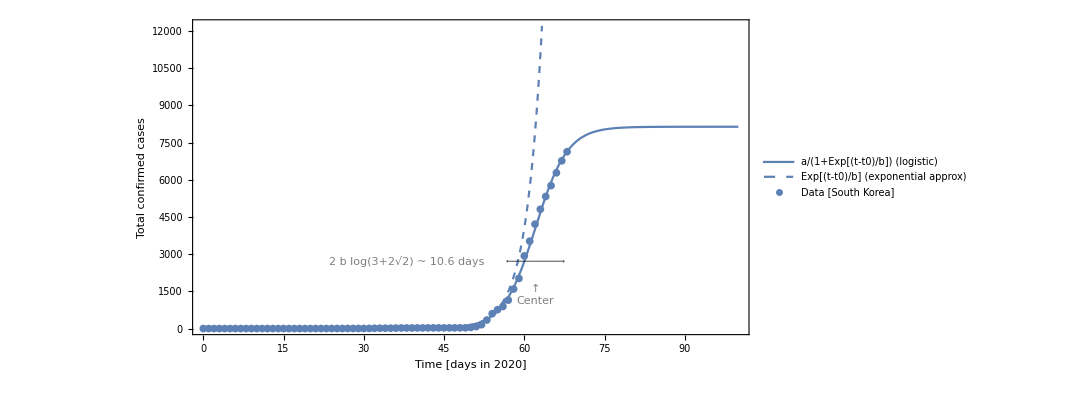

```mathematica
Show[
Plot[{test,firstOrder},{t,0,100},PlotRange->({0,1.5a0}/.params),ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,True,True},PlotStyle->{Automatic,Directive[ColorData[97][1],Dashed]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{"Time [days in 2020]\n","Total confirmed cases","",""},Epilog->{Thick,
Opacity[0.5],
Text["2 b log(3+2√2) ~ "<>ToString[Round[width,0.1]]<>" days",{t0-8b0,a0/(b0 )}/.params],
Text["↑\nCenter",{t0,0.5a0/b0}/.params],
Line[{{t0-Log[3+2 √2]b0,a0/b0},{t0+Log[3+2 √2]b0,a0/b0}}/.params],
Line[{{t0-Log[3+2 √2]b0,a0/b0+50},{t0-Log[3+2 √2]b0,a0/b0-50}}/.params],
Line[{{t0+Log[3+2 √2]b0,a0/b0+50},{t0+Log[3+2 √2]b0,a0/b0-50}}/.params]
},PlotLegends->{"a/(1+Exp[(t-t0)/b]) (logistic)","Exp[(t-t0)/b] (exponential approx)"}],
ListPlot[{
{(#[[1]]-2020+0.00219035)*365.24,(1/scale)#[[2]]}&/@accumulatedKorea
},PlotStyle->{PointSize[0.007],Directive[PointSize[0.007],ColorData[97][4]]},PlotLegends->{"Data [South Korea]"}]]
```

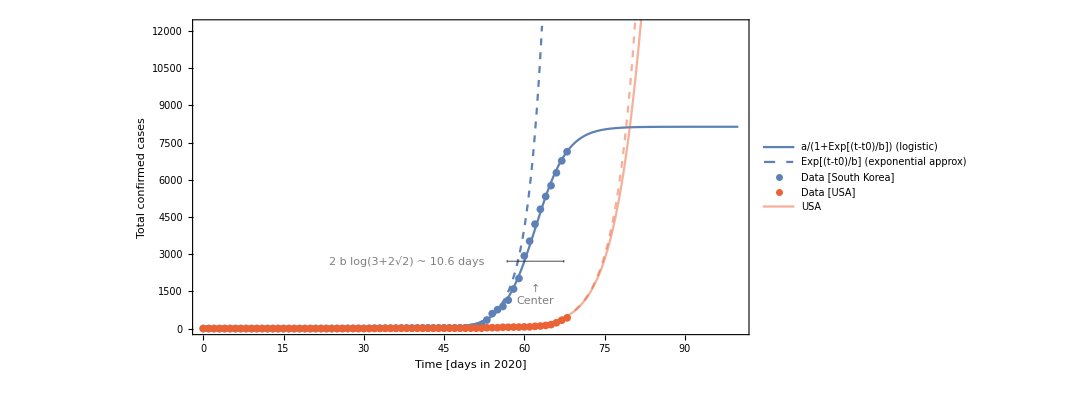

```mathematica
Show[
Plot[{test,firstOrder},{t,0,100},PlotRange->({0,1.5a0}/.params),ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,True,True},PlotStyle->{Automatic,Directive[ColorData[97][1],Dashed]},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameLabel->{"Time [days in 2020]\n","Total confirmed cases","",""},Epilog->{Thick,
Opacity[0.5],
Text["2 b log(3+2√2) ~ "<>ToString[Round[width,0.1]]<>" days",{t0-8b0,a0/(b0 )}/.params],
Text["↑\nCenter",{t0,0.5a0/b0}/.params],
Line[{{t0-Log[3+2 √2]b0,a0/b0},{t0+Log[3+2 √2]b0,a0/b0}}/.params],
Line[{{t0-Log[3+2 √2]b0,a0/b0+50},{t0-Log[3+2 √2]b0,a0/b0-50}}/.params],
Line[{{t0+Log[3+2 √2]b0,a0/b0+50},{t0+Log[3+2 √2]b0,a0/b0-50}}/.params]
},PlotLegends->{"a/(1+Exp[(t-t0)/b]) (logistic)","Exp[(t-t0)/b] (exponential approx)"}],
ListPlot[{
{(#[[1]]-2020+0.00219035)*365.24,(1/scale)#[[2]]}&/@accumulatedKorea,
{(#[[1]]-2020+0.00219035)*365.24,(1/scale)#[[2]]}&/@accumulatedUSA
},PlotStyle->{PointSize[0.007],Directive[PointSize[0.007],ColorData[97][4]]},PlotLegends->{"Data [South Korea]","Data [USA]"}],

Plot[{funcUSA/.t->tt/365.24+2020,(51753.19055386672 ⅇ^(-91.64028214226228 (2020.236614693027-t)))/.t->tt/365.24+2020},{tt,0,100},PlotStyle->{Directive[ColorData[97][4],Opacity[0.5]],Directive[Dashed,ColorData[97][4],Opacity[0.5]]},PlotLegends->{"USA"}]]
```

```mathematica
funcUSA
```

51753.2/(1+ⅇ^(91.6403 (2020.24-t)))

```mathematica
1/(91.64028214226228)
%*365.24
%*Log[3+2 √2]*2
```

0.0109122

3.98558

14.0512

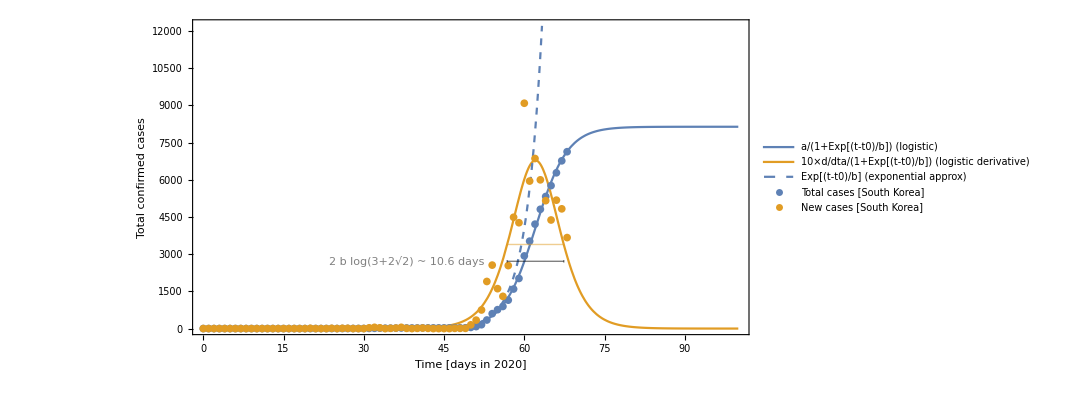

```mathematica
Show[
Plot[{test,10der,firstOrder},{t,0,100},PlotRange->({0,1.5a0}/.params),ImageSize->11*72,AspectRatio->1/2,BaseStyle->FontSize->15,Frame->{True,True,True,True},PlotStyle->{Automatic,Automatic,Directive[ColorData[97][1],Dashed]},FrameTicks->{{Automatic,Table[{ii,ii/10},{ii,0,1.5a0/.params,2000}]},{Automatic,Automatic}},FrameLabel->{"Time [days in 2020]\n","Total confirmed cases","","New confirmed cases"},Epilog->{Thick,
Opacity[0.5],
Text["2 b log(3+2√2) ~ "<>ToString[Round[width,0.1]]<>" days",{t0-8b0,a0/(b0 )}/.params],

Line[{{t0-Log[3+2 √2]b0,a0/b0},{t0+Log[3+2 √2]b0,a0/b0}}/.params],
Line[{{t0-Log[3+2 √2]b0,a0/b0+50},{t0-Log[3+2 √2]b0,a0/b0-50}}/.params],
Line[{{t0+Log[3+2 √2]b0,a0/b0+50},{t0+Log[3+2 √2]b0,a0/b0-50}}/.params],
ColorData[97][2],Line[{{t0-Log[3+2 √2]b0,10a0/(b0 8)},{t0+Log[3+2 √2]b0,10a0/(b0 8)}}/.params]
},PlotLegends->{"a/(1+Exp[(t-t0)/b]) (logistic)","10×d/dta/(1+Exp[(t-t0)/b]) (logistic derivative)","Exp[(t-t0)/b] (exponential approx)"}],
ListPlot[{
{(#[[1]]-2020+0.00219035)*365.24,(1/scale)#[[2]]}&/@accumulatedKorea,
{(#[[1]]-2020+0.00219035)*365.24,10#[[2]]}&/@totalsKorea
},PlotStyle->PointSize[0.007],PlotLegends->{"Total cases [South Korea]","New cases [South Korea]"}]]
```